```mathematica
(*Вариант 6*)
(*Задание 1*)
```

```mathematica
f[x_]=(Log[2,3x+2])^2/(x+4); 
x0 = 1.13;
(*Пункт а)*)
D[f[x],x]
D[f[x],{x,2}]
```

(6 Log[2+3 x])/((4+x) (2+3 x) Log[2]^2)-Log[2+3 x]^2/((4+x)^2 Log[2]^2)

-(12 Log[2+3 x])/((4+x)^2 (2+3 x) Log[2]^2)+(2 Log[2+3 x]^2)/((4+x)^3 Log[2]^2)+(18/(2+3 x)^2-(18 Log[2+3 x])/(2+3 x)^2)/((4+x) Log[2]^2)

```mathematica
valueD1 = D[f[x], x]/.x->x0 
valueD2 = D[f[x], {x,2}]/.x->x0
```

0.536382

-0.381195

```mathematica
(*Пункт б)*)
delta1[x_, h_]=f[x+h] - f[x];
delta2[x_, h_]=f[x+2 h]-2 f[x+h]+f[x];
delta3[x_, h_]= f[x+3 h]-3 f[x+2 h]+3 f[x+h]-f[x];

d1 [x_,h_] = 1/h(delta1[x, h] - 1/2 delta2[x, h] +1/3 delta3[x, h] );
d2[x_, h_] = 1/h^2(delta2[x, h]-delta3[x, h]);
h1 = 0.1;
valued11 = d1[x0,h1]
```

0.536341

```mathematica
valued21 = d2[x0,h1]
```

-0.379704

```mathematica
h2 = 0.01;
valued12 = d1[x0,h2]
```

0.536382

```mathematica
valued22 = d2[x0,h2]
```

-0.381182

```mathematica
(*Задание 2*)
(*Пункт а)*)
f[x_]=Sin[x+Cos[x]]; 
a =-1;
b= 3;
h = 0.2;
n = (b-a)/h;
d1[x_]=(f[x+h]-f[x])/h;
Table [{a+h*i,d1[a+h*i]},{i,0,n}]
```

{{-1.,1.70284},{-0.8,1.63272},{-0.6,1.37184},{-0.4,1.02763},{-0.2,0.690721},{0.,0.415802},{0.2,0.221732},{0.4,0.102307},{0.6,0.0390869},{0.8,0.0113924},{1.,0.00214651},{1.2,0.000176304},{1.4,1.71882×10^-6},{1.6,-0.0000100157},{1.8,-0.000416181},{2.,-0.00371498},{2.2,-0.0169167},{2.4,-0.0529897},{2.6,-0.130439},{2.8,-0.270077},{3.,-0.487978}}

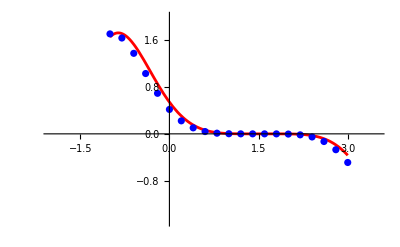

```mathematica
(*Пункт б)*)
dif[x_]=D[f[x],x];
graphD = Plot[dif[x],{x,a,b},PlotRange->{{-2,3.5},{-1.5,2}},PlotStyle->Red];
graphd = ListPlot[Table[{a+h*i,d1[a+h*i]},{i,0,n}],PlotStyle->Blue];
Show[graphD,graphd]
```

```mathematica
(*Задание 3*)
```

```mathematica
f[x_]= (1+√(2.3 x^2+0.2))/(2.4+√(1.6x+1.7));
a = 0.7;
b= 2.1;
(*Пункт а)*)
n = 8;
h = (b-a)/n;
Int1 = h*Sum[f[a+(h*i)/2+(h*(i-1))/2], {i,1,n}]
```

1.00925

```mathematica
n = 10;
h =(b-a)/n;
Int2 = h*Sum[f[a+(h*i)/2+(h*(i-1))/2], {i,1,n}]
```

1.00924

```mathematica
Int = Int2+64/36*(Int2-Int1)
```

1.00921

```mathematica
n =8;
h =(b-a)/n;
Int1 = h*(f[a]/2+Sum[f[a+h*i],{i,1,n-1}] + f[b]/2)
```

1.00914

```mathematica
n = 10;
h=(b-a)/n;
Int2 = h*(f[a]/2+Sum[f[a+h*i],{i,1,n-1}] + f[b]/2)
```

1.00917

```mathematica
Int = Int2+64/36*(Int2-Int1)
```

1.00922

```mathematica
(*Задание 4*)
X16 = {{0.5,1.2506},{0.552,1.2938},{0.604,1.3828},{0.656,1.4115},{0.708,1.4927},{0.76,1.5111},{0.812,1.5877},{0.864,1.5993},{0.916,1.6742},{0.968,1.6819},{1.02,1.7575},{1.072,1.7640},{1.124,1.8428},{1.176,1.8501},{1.228,1.9344},{1.28,1.9446},{1.332,2.0366}};
X8 = Table[X16[[i]],{i,1,17,2}];
n =8;
 h=(X8[[9,1]]-X8[[1,1]])/n;
value1 = h/3*(X8[[1, 2]] + X8[[9, 2]] + 4 * Sum[X8[[i+1, 2]],{i, 1, n - 1,2}] + 2 * Sum[X8[[i+1, 2]],{i,  2, n - 2, 2}])
```

1.38515

```mathematica
n=16;h=(X16[[17,1]]-X16[[1,1]])/n;
value2 =h/3*(X16[[1, 2]] + X16[[17, 2]] + 4 * Sum[X16[[i+1, 2]],{i, 1, n - 1,2}] + 2 * Sum[X16[[i+1, 2]],{i,  2, n - 2, 2}])
```

1.36685

```mathematica
(*Задание 5*)
f[x_]= Cosh[x+3]/(5x+2);
n= 7;
a = 1.3;
b =2.6;
sl = NSolve[LegendreP[n,t]==0,t];
listt = t/.sl
```

{-0.949108,-0.741531,-0.405845,0.,0.405845,0.741531,0.949108}

```mathematica
MatrixForm[T=Table[If[i==1,1,(listt[[j]])^(i-1)],{i,n},{j,n}]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
-0.949108 | -0.741531 | -0.405845 | 0. | 0.405845 | 0.741531 | 0.949108
0.900806 | 0.549868 | 0.16471 | 0. | 0.16471 | 0.549868 | 0.900806
-0.854962 | -0.407745 | -0.0668469 | 0. | 0.0668469 | 0.407745 | 0.854962
0.811451 | 0.302355 | 0.0271295 | 0. | 0.0271295 | 0.302355 | 0.811451
-0.770155 | -0.224206 | -0.0110104 | 0. | 0.0110104 | 0.224206 | 0.770155
0.73096 | 0.166256 | 0.0044685 | 0. | 0.0044685 | 0.166256 | 0.73096)

```mathematica
B=Table[If[EvenQ[i]==True, 0, 2/i], {i, n}]//N
```

{2.,0.,0.666667,0.,0.4,0.,0.285714}

```mathematica
A = LinearSolve[T,B]
```

{0.129485,0.279705,0.38183,0.417959,0.38183,0.279705,0.129485}

```mathematica
PaddedForm[int= (b-a)/2∑_(i=1)^n (A[[i]]*f[(b+a)/2+(b-a)/2*listt[[i]]]),{19,18}]
```

8.096027374414600000